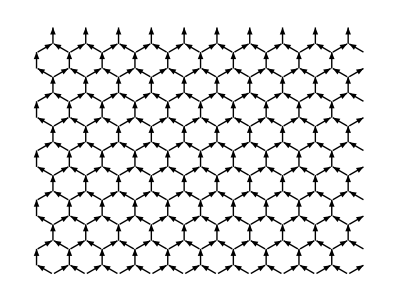

```mathematica
PlotArrays[lst_]:=Graphics[Table[Arrow[lst[[x]]],{x,Length[lst]}]];(*Я написал свою функцию PlotArrays для построения графика. Тут она объявляется *)
spins={
{{{2,0.25},{2,1.25}},{{2,3.25},{2,4.25}},{{2,6.25},{2,7.25}},{{2,9.25},{2,10.25}},{{2,12.25},{2,13.25}},{{1.93301,1.25},{1.06699,1.75}},{{1.93301,4.25},{1.06699,4.75}},{{1.93301,7.25},{1.06699,7.75}},{{1.93301,10.25},{1.06699,10.75}},{{1.93301,13.25},{1.06699,13.75}},{{0.0669873,1.25},{0.933013,1.75}},{{0.0669873,4.25},{0.933013,4.75}},{{0.0669873,7.25},{0.933013,7.75}},{{0.0669873,10.25},{0.933013,10.75}},{{0.0669873,13.25},{0.933013,13.75}},{{0,0.25},{0,1.25}},{{0,3.25},{0,4.25}},{{0,6.25},{0,7.25}},{{0,9.25},{0,10.25}},{{0,12.25},{0,13.25}},{{0.933013,-0.25},{0.0669873,0.25}},{{0.933013,2.75},{0.0669873,3.25}},{{0.933013,5.75},{0.0669873,6.25}},{{0.933013,8.75},{0.0669873,9.25}},{{0.933013,11.75},{0.0669873,12.25}},{{1.06699,-0.25},{1.93301,0.25}},{{1.06699,2.75},{1.93301,3.25}},{{1.06699,5.75},{1.93301,6.25}},{{1.06699,8.75},{1.93301,9.25}},{{1.06699,11.75},{1.93301,12.25}},{{3.93301,1.25},{3.06699,1.75}},{{3.93301,4.25},{3.06699,4.75}},{{3.93301,7.25},{3.06699,7.75}},{{3.93301,10.25},{3.06699,10.75}},{{3.93301,13.25},{3.06699,13.75}},{{2.06699,1.25},{2.93301,1.75}},{{2.93301,-0.25},{2.06699,0.25}},{{2.06699,4.25},{2.93301,4.75}},{{2.93301,2.75},{2.06699,3.25}},{{2.06699,7.25},{2.93301,7.75}},{{2.93301,5.75},{2.06699,6.25}},{{2.06699,10.25},{2.93301,10.75}},{{2.93301,8.75},{2.06699,9.25}},{{2.06699,13.25},{2.93301,13.75}},{{2.93301,11.75},{2.06699,12.25}},{{3.06699,-0.25},{3.93301,0.25}},{{3.06699,2.75},{3.93301,3.25}},{{3.06699,5.75},{3.93301,6.25}},{{3.06699,8.75},{3.93301,9.25}},{{3.06699,11.75},{3.93301,12.25}},{{1,1.75},{1,2.75}},{{1,4.75},{1,5.75}},{{1,7.75},{1,8.75}},{{1,10.75},{1,11.75}},{{1,13.75},{1,14.75}},{{3,1.75},{3,2.75}},{{3,4.75},{3,5.75}},{{3,7.75},{3,8.75}},{{3,10.75},{3,11.75}},{{3,13.75},{3,14.75}},{{6,0.25},{6,1.25}},{{6,3.25},{6,4.25}},{{6,6.25},{6,7.25}},{{6,9.25},{6,10.25}},{{6,12.25},{6,13.25}},{{5.93301,1.25},{5.06699,1.75}},{{5.93301,4.25},{5.06699,4.75}},{{5.93301,7.25},{5.06699,7.75}},{{5.93301,10.25},{5.06699,10.75}},{{5.93301,13.25},{5.06699,13.75}},{{4.06699,1.25},{4.93301,1.75}},{{4.06699,4.25},{4.93301,4.75}},{{4.06699,7.25},{4.93301,7.75}},{{4.06699,10.25},{4.93301,10.75}},{{4.06699,13.25},{4.93301,13.75}},{{4,0.25},{4,1.25}},{{4,3.25},{4,4.25}},{{4,6.25},{4,7.25}},{{4,9.25},{4,10.25}},{{4,12.25},{4,13.25}},{{4.93301,-0.25},{4.06699,0.25}},{{4.93301,2.75},{4.06699,3.25}},{{4.93301,5.75},{4.06699,6.25}},{{4.93301,8.75},{4.06699,9.25}},{{4.93301,11.75},{4.06699,12.25}},{{5.06699,-0.25},{5.93301,0.25}},{{5.06699,2.75},{5.93301,3.25}},{{5.06699,5.75},{5.93301,6.25}},{{5.06699,8.75},{5.93301,9.25}},{{5.06699,11.75},{5.93301,12.25}},{{7.93301,1.25},{7.06699,1.75}},{{7.93301,4.25},{7.06699,4.75}},{{7.93301,7.25},{7.06699,7.75}},{{7.93301,10.25},{7.06699,10.75}},{{7.93301,13.25},{7.06699,13.75}},{{6.06699,1.25},{6.93301,1.75}},{{6.93301,-0.25},{6.06699,0.25}},{{6.06699,4.25},{6.93301,4.75}},{{6.93301,2.75},{6.06699,3.25}},{{6.06699,7.25},{6.93301,7.75}},{{6.93301,5.75},{6.06699,6.25}},{{6.06699,10.25},{6.93301,10.75}},{{6.93301,8.75},{6.06699,9.25}},{{6.06699,13.25},{6.93301,13.75}},{{6.93301,11.75},{6.06699,12.25}},{{7.06699,-0.25},{7.93301,0.25}},{{7.06699,2.75},{7.93301,3.25}},{{7.06699,5.75},{7.93301,6.25}},{{7.06699,8.75},{7.93301,9.25}},{{7.06699,11.75},{7.93301,12.25}},{{5,1.75},{5,2.75}},{{5,4.75},{5,5.75}},{{5,7.75},{5,8.75}},{{5,10.75},{5,11.75}},{{5,13.75},{5,14.75}},{{7,1.75},{7,2.75}},{{7,4.75},{7,5.75}},{{7,7.75},{7,8.75}},{{7,10.75},{7,11.75}},{{7,13.75},{7,14.75}},{{10,0.25},{10,1.25}},{{10,3.25},{10,4.25}},{{10,6.25},{10,7.25}},{{10,9.25},{10,10.25}},{{10,12.25},{10,13.25}},{{9.93301,1.25},{9.06699,1.75}},{{9.93301,4.25},{9.06699,4.75}},{{9.93301,7.25},{9.06699,7.75}},{{9.93301,10.25},{9.06699,10.75}},{{9.93301,13.25},{9.06699,13.75}},{{8.06699,1.25},{8.93301,1.75}},{{8.06699,4.25},{8.93301,4.75}},{{8.06699,7.25},{8.93301,7.75}},{{8.06699,10.25},{8.93301,10.75}},{{8.06699,13.25},{8.93301,13.75}},{{8,0.25},{8,1.25}},{{8,3.25},{8,4.25}},{{8,6.25},{8,7.25}},{{8,9.25},{8,10.25}},{{8,12.25},{8,13.25}},{{8.93301,-0.25},{8.06699,0.25}},{{8.93301,2.75},{8.06699,3.25}},{{8.93301,5.75},{8.06699,6.25}},{{8.93301,8.75},{8.06699,9.25}},{{8.93301,11.75},{8.06699,12.25}},{{9.06699,-0.25},{9.93301,0.25}},{{9.06699,2.75},{9.93301,3.25}},{{9.06699,5.75},{9.93301,6.25}},{{9.06699,8.75},{9.93301,9.25}},{{9.06699,11.75},{9.93301,12.25}},{{11.933,1.25},{11.067,1.75}},{{11.933,4.25},{11.067,4.75}},{{11.933,7.25},{11.067,7.75}},{{11.933,10.25},{11.067,10.75}},{{11.933,13.25},{11.067,13.75}},{{10.067,1.25},{10.933,1.75}},{{10.933,-0.25},{10.067,0.25}},{{10.067,4.25},{10.933,4.75}},{{10.933,2.75},{10.067,3.25}},{{10.067,7.25},{10.933,7.75}},{{10.933,5.75},{10.067,6.25}},{{10.067,10.25},{10.933,10.75}},{{10.933,8.75},{10.067,9.25}},{{10.067,13.25},{10.933,13.75}},{{10.933,11.75},{10.067,12.25}},{{11.067,-0.25},{11.933,0.25}},{{11.067,2.75},{11.933,3.25}},{{11.067,5.75},{11.933,6.25}},{{11.067,8.75},{11.933,9.25}},{{11.067,11.75},{11.933,12.25}},{{9,1.75},{9,2.75}},{{9,4.75},{9,5.75}},{{9,7.75},{9,8.75}},{{9,10.75},{9,11.75}},{{9,13.75},{9,14.75}},{{11,1.75},{11,2.75}},{{11,4.75},{11,5.75}},{{11,7.75},{11,8.75}},{{11,10.75},{11,11.75}},{{11,13.75},{11,14.75}},{{14,0.25},{14,1.25}},{{14,3.25},{14,4.25}},{{14,6.25},{14,7.25}},{{14,9.25},{14,10.25}},{{14,12.25},{14,13.25}},{{13.933,1.25},{13.067,1.75}},{{13.933,4.25},{13.067,4.75}},{{13.933,7.25},{13.067,7.75}},{{13.933,10.25},{13.067,10.75}},{{13.933,13.25},{13.067,13.75}},{{12.067,1.25},{12.933,1.75}},{{12.067,4.25},{12.933,4.75}},{{12.067,7.25},{12.933,7.75}},{{12.067,10.25},{12.933,10.75}},{{12.067,13.25},{12.933,13.75}},{{12,0.25},{12,1.25}},{{12,3.25},{12,4.25}},{{12,6.25},{12,7.25}},{{12,9.25},{12,10.25}},{{12,12.25},{12,13.25}},{{12.933,-0.25},{12.067,0.25}},{{12.933,2.75},{12.067,3.25}},{{12.933,5.75},{12.067,6.25}},{{12.933,8.75},{12.067,9.25}},{{12.933,11.75},{12.067,12.25}},{{13.067,-0.25},{13.933,0.25}},{{13.067,2.75},{13.933,3.25}},{{13.067,5.75},{13.933,6.25}},{{13.067,8.75},{13.933,9.25}},{{13.067,11.75},{13.933,12.25}},{{15.933,1.25},{15.067,1.75}},{{15.933,4.25},{15.067,4.75}},{{15.933,7.25},{15.067,7.75}},{{15.933,10.25},{15.067,10.75}},{{15.933,13.25},{15.067,13.75}},{{14.067,1.25},{14.933,1.75}},{{14.933,-0.25},{14.067,0.25}},{{14.067,4.25},{14.933,4.75}},{{14.933,2.75},{14.067,3.25}},{{14.067,7.25},{14.933,7.75}},{{14.933,5.75},{14.067,6.25}},{{14.067,10.25},{14.933,10.75}},{{14.933,8.75},{14.067,9.25}},{{14.067,13.25},{14.933,13.75}},{{14.933,11.75},{14.067,12.25}},{{15.067,-0.25},{15.933,0.25}},{{15.067,2.75},{15.933,3.25}},{{15.067,5.75},{15.933,6.25}},{{15.067,8.75},{15.933,9.25}},{{15.067,11.75},{15.933,12.25}},{{13,1.75},{13,2.75}},{{13,4.75},{13,5.75}},{{13,7.75},{13,8.75}},{{13,10.75},{13,11.75}},{{13,13.75},{13,14.75}},{{15,1.75},{15,2.75}},{{15,4.75},{15,5.75}},{{15,7.75},{15,8.75}},{{15,10.75},{15,11.75}},{{15,13.75},{15,14.75}},{{18,0.25},{18,1.25}},{{18,3.25},{18,4.25}},{{18,6.25},{18,7.25}},{{18,9.25},{18,10.25}},{{18,12.25},{18,13.25}},{{17.933,1.25},{17.067,1.75}},{{17.933,4.25},{17.067,4.75}},{{17.933,7.25},{17.067,7.75}},{{17.933,10.25},{17.067,10.75}},{{17.933,13.25},{17.067,13.75}},{{16.067,1.25},{16.933,1.75}},{{16.067,4.25},{16.933,4.75}},{{16.067,7.25},{16.933,7.75}},{{16.067,10.25},{16.933,10.75}},{{16.067,13.25},{16.933,13.75}},{{16,0.25},{16,1.25}},{{16,3.25},{16,4.25}},{{16,6.25},{16,7.25}},{{16,9.25},{16,10.25}},{{16,12.25},{16,13.25}},{{16.933,-0.25},{16.067,0.25}},{{16.933,2.75},{16.067,3.25}},{{16.933,5.75},{16.067,6.25}},{{16.933,8.75},{16.067,9.25}},{{16.933,11.75},{16.067,12.25}},{{17.067,-0.25},{17.933,0.25}},{{17.067,2.75},{17.933,3.25}},{{17.067,5.75},{17.933,6.25}},{{17.067,8.75},{17.933,9.25}},{{17.067,11.75},{17.933,12.25}},{{19.933,1.25},{19.067,1.75}},{{19.933,4.25},{19.067,4.75}},{{19.933,7.25},{19.067,7.75}},{{19.933,10.25},{19.067,10.75}},{{19.933,13.25},{19.067,13.75}},{{18.067,1.25},{18.933,1.75}},{{18.933,-0.25},{18.067,0.25}},{{18.067,4.25},{18.933,4.75}},{{18.933,2.75},{18.067,3.25}},{{18.067,7.25},{18.933,7.75}},{{18.933,5.75},{18.067,6.25}},{{18.067,10.25},{18.933,10.75}},{{18.933,8.75},{18.067,9.25}},{{18.067,13.25},{18.933,13.75}},{{18.933,11.75},{18.067,12.25}},{{19.067,-0.25},{19.933,0.25}},{{19.067,2.75},{19.933,3.25}},{{19.067,5.75},{19.933,6.25}},{{19.067,8.75},{19.933,9.25}},{{19.067,11.75},{19.933,12.25}},{{17,1.75},{17,2.75}},{{17,4.75},{17,5.75}},{{17,7.75},{17,8.75}},{{17,10.75},{17,11.75}},{{17,13.75},{17,14.75}},{{19,1.75},{19,2.75}},{{19,4.75},{19,5.75}},{{19,7.75},{19,8.75}},{{19,10.75},{19,11.75}},{{19,13.75},{19,14.75}}}

};
fig1=PlotArrays[spins]
```

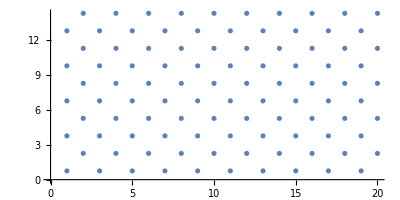

```mathematica
centers={
{{1,0.75},{1,3.75},{1,6.75},{1,9.75},{1,12.75},{3,0.75},{3,3.75},{3,6.75},{3,9.75},{3,12.75},{2,2.25},{2,5.25},{2,8.25},{2,11.25},{2,14.25},{4,2.25},{4,5.25},{4,8.25},{4,11.25},{4,14.25},{5,0.75},{5,3.75},{5,6.75},{5,9.75},{5,12.75},{7,0.75},{7,3.75},{7,6.75},{7,9.75},{7,12.75},{6,2.25},{6,5.25},{6,8.25},{6,11.25},{6,14.25},{8,2.25},{8,5.25},{8,8.25},{8,11.25},{8,14.25},{9,0.75},{9,3.75},{9,6.75},{9,9.75},{9,12.75},{11,0.75},{11,3.75},{11,6.75},{11,9.75},{11,12.75},{10,2.25},{10,5.25},{10,8.25},{10,11.25},{10,14.25},{12,2.25},{12,5.25},{12,8.25},{12,11.25},{12,14.25},{13,0.75},{13,3.75},{13,6.75},{13,9.75},{13,12.75},{15,0.75},{15,3.75},{15,6.75},{15,9.75},{15,12.75},{14,2.25},{14,5.25},{14,8.25},{14,11.25},{14,14.25},{16,2.25},{16,5.25},{16,8.25},{16,11.25},{16,14.25},{17,0.75},{17,3.75},{17,6.75},{17,9.75},{17,12.75},{19,0.75},{19,3.75},{19,6.75},{19,9.75},{19,12.75},{18,2.25},{18,5.25},{18,8.25},{18,11.25},{18,14.25},{20,2.25},{20,5.25},{20,8.25},{20,11.25},{20,14.25}}



};
fig2=ListPlot[centers,AspectRatio->1/2]
```

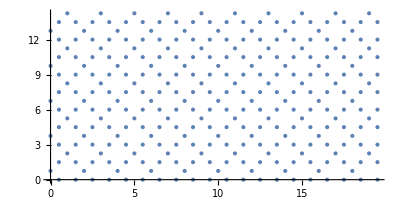

```mathematica
coord={
{{2,0.75},{2,3.75},{2,6.75},{2,9.75},{2,12.75},{1.5,1.5},{1.5,4.5},{1.5,7.5},{1.5,10.5},{1.5,13.5},{0.5,1.5},{0.5,4.5},{0.5,7.5},{0.5,10.5},{0.5,13.5},{0,0.75},{0,3.75},{0,6.75},{0,9.75},{0,12.75},{0.5,0},{0.5,3},{0.5,6},{0.5,9},{0.5,12},{1.5,0},{1.5,3},{1.5,6},{1.5,9},{1.5,12},{3.5,1.5},{3.5,4.5},{3.5,7.5},{3.5,10.5},{3.5,13.5},{2.5,1.5},{2.5,0},{2.5,4.5},{2.5,3},{2.5,7.5},{2.5,6},{2.5,10.5},{2.5,9},{2.5,13.5},{2.5,12},{3.5,0},{3.5,3},{3.5,6},{3.5,9},{3.5,12},{1,2.25},{1,5.25},{1,8.25},{1,11.25},{1,14.25},{3,2.25},{3,5.25},{3,8.25},{3,11.25},{3,14.25},{6,0.75},{6,3.75},{6,6.75},{6,9.75},{6,12.75},{5.5,1.5},{5.5,4.5},{5.5,7.5},{5.5,10.5},{5.5,13.5},{4.5,1.5},{4.5,4.5},{4.5,7.5},{4.5,10.5},{4.5,13.5},{4,0.75},{4,3.75},{4,6.75},{4,9.75},{4,12.75},{4.5,0},{4.5,3},{4.5,6},{4.5,9},{4.5,12},{5.5,0},{5.5,3},{5.5,6},{5.5,9},{5.5,12},{7.5,1.5},{7.5,4.5},{7.5,7.5},{7.5,10.5},{7.5,13.5},{6.5,1.5},{6.5,0},{6.5,4.5},{6.5,3},{6.5,7.5},{6.5,6},{6.5,10.5},{6.5,9},{6.5,13.5},{6.5,12},{7.5,0},{7.5,3},{7.5,6},{7.5,9},{7.5,12},{5,2.25},{5,5.25},{5,8.25},{5,11.25},{5,14.25},{7,2.25},{7,5.25},{7,8.25},{7,11.25},{7,14.25},{10,0.75},{10,3.75},{10,6.75},{10,9.75},{10,12.75},{9.5,1.5},{9.5,4.5},{9.5,7.5},{9.5,10.5},{9.5,13.5},{8.5,1.5},{8.5,4.5},{8.5,7.5},{8.5,10.5},{8.5,13.5},{8,0.75},{8,3.75},{8,6.75},{8,9.75},{8,12.75},{8.5,0},{8.5,3},{8.5,6},{8.5,9},{8.5,12},{9.5,0},{9.5,3},{9.5,6},{9.5,9},{9.5,12},{11.5,1.5},{11.5,4.5},{11.5,7.5},{11.5,10.5},{11.5,13.5},{10.5,1.5},{10.5,0},{10.5,4.5},{10.5,3},{10.5,7.5},{10.5,6},{10.5,10.5},{10.5,9},{10.5,13.5},{10.5,12},{11.5,0},{11.5,3},{11.5,6},{11.5,9},{11.5,12},{9,2.25},{9,5.25},{9,8.25},{9,11.25},{9,14.25},{11,2.25},{11,5.25},{11,8.25},{11,11.25},{11,14.25},{14,0.75},{14,3.75},{14,6.75},{14,9.75},{14,12.75},{13.5,1.5},{13.5,4.5},{13.5,7.5},{13.5,10.5},{13.5,13.5},{12.5,1.5},{12.5,4.5},{12.5,7.5},{12.5,10.5},{12.5,13.5},{12,0.75},{12,3.75},{12,6.75},{12,9.75},{12,12.75},{12.5,0},{12.5,3},{12.5,6},{12.5,9},{12.5,12},{13.5,0},{13.5,3},{13.5,6},{13.5,9},{13.5,12},{15.5,1.5},{15.5,4.5},{15.5,7.5},{15.5,10.5},{15.5,13.5},{14.5,1.5},{14.5,0},{14.5,4.5},{14.5,3},{14.5,7.5},{14.5,6},{14.5,10.5},{14.5,9},{14.5,13.5},{14.5,12},{15.5,0},{15.5,3},{15.5,6},{15.5,9},{15.5,12},{13,2.25},{13,5.25},{13,8.25},{13,11.25},{13,14.25},{15,2.25},{15,5.25},{15,8.25},{15,11.25},{15,14.25},{18,0.75},{18,3.75},{18,6.75},{18,9.75},{18,12.75},{17.5,1.5},{17.5,4.5},{17.5,7.5},{17.5,10.5},{17.5,13.5},{16.5,1.5},{16.5,4.5},{16.5,7.5},{16.5,10.5},{16.5,13.5},{16,0.75},{16,3.75},{16,6.75},{16,9.75},{16,12.75},{16.5,0},{16.5,3},{16.5,6},{16.5,9},{16.5,12},{17.5,0},{17.5,3},{17.5,6},{17.5,9},{17.5,12},{19.5,1.5},{19.5,4.5},{19.5,7.5},{19.5,10.5},{19.5,13.5},{18.5,1.5},{18.5,0},{18.5,4.5},{18.5,3},{18.5,7.5},{18.5,6},{18.5,10.5},{18.5,9},{18.5,13.5},{18.5,12},{19.5,0},{19.5,3},{19.5,6},{19.5,9},{19.5,12},{17,2.25},{17,5.25},{17,8.25},{17,11.25},{17,14.25},{19,2.25},{19,5.25},{19,8.25},{19,11.25},{19,14.25}}





};

fig3=ListPlot[coord,AspectRatio->1/2]
```

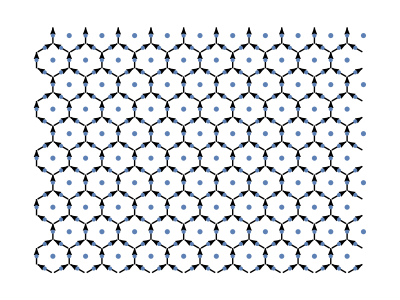

```mathematica
Show[fig1,fig2,fig3]
```

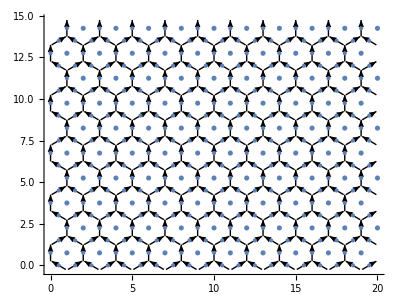

```mathematica
Show[%23,Axes->True,AxesStyle->Gray]
```

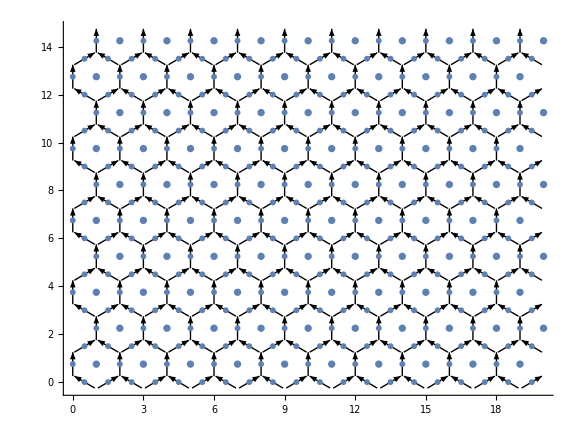

```mathematica
Show[%24,ImageSize->Large]
```